```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
colorf=Blend[{Blue,Red},#]&;
colorRainbow=ColorData["Rainbow"];
colorTemp=ColorData["Temperature"];
plotLegend[{min_,max_},n_,col_]:=Graphics[{{col[(#-1)/(n-1)],Rectangle[{0,#-1},{1,#}]},{Black,Text[NumberForm[Rescale[#,{1,n},{min,max}],{4,2}],{3,#-.5},{1,0}]}}&/@Range@n,Frame->True,FrameTicks->None,PlotRangePadding->.5]
```

## Define Beams

```mathematica
spectDBWC1={{1,-0.6},{1,0.1},{1,0.6}}
spectDBWC2={{0.5,-0.6},{1,0.1},{1,0.6}}
spectDBWC3={{0.1,-0.6},{1,0.1},{1,0.6}}
```

{{1,-0.6},{1,0.1},{1,0.6}}

{{0.5,-0.6},{1,0.1},{1,0.6}}

{{0.1,-0.6},{1,0.1},{1,0.6}}

```mathematica
spectDBC1={{-1,-0.6},{1,0.1},{1,0.6}}
spectDBC2={{-0.5,-0.6},{1,0.1},{1,0.6}}
spectDBC3={{-0.1,-0.6},{1,0.1},{1,0.6}}
```

{{-1,-0.6},{1,0.1},{1,0.6}}

{{-0.5,-0.6},{1,0.1},{1,0.6}}

{{-0.1,-0.6},{1,0.1},{1,0.6}}

```mathematica
spectDBWC4={{0.5,-0.1},{1,0.4},{1,0.6}}
spectDBC4={{-0.5,0.1},{1,0.4},{1,0.6}}
```

{{0.5,-0.1},{1,0.4},{1,0.6}}

{{-0.5,0.1},{1,0.4},{1,0.6}}

## Define Useful Functions

```mathematica
DBPltDRMAA[spect_,pltRange_:{{-2,2},{-2,2}}]:=Module[{spectM},

spectM=spect;

ParametricPlot[
{DBAxialSymKNMAA[spectM, n],DBAxialSymOmegaNMAA[spectM, n]},
{n,-50,50},
PlotRange->pltRange,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"DR for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
DBPltDRMAAData[spect_,discret_:0.01]:=Module[{spectM},

spectM=spect;

Table[
{DBAxialSymKNMAA[spectM, n],DBAxialSymOmegaNMAA[spectM, n]},
{n,-50,50,discret}
]
]
```

```mathematica
DBPltDRMZA[spect_,pltRange_:{{-2,2},{-2,2}}]:=Module[{spectM},

spectM=spect;

ParametricPlot[
Evaluate[
{n #, #} &/@DBAxialSymOmegaNMZA[spectM, n]
],
{n,-50,50},
PlotRange->pltRange,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"DR for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"},PlotLegends->Placed[{"MZA+","MZA-"},{Above,Center}]
]
]
```

```mathematica
DBPltDRMZAData[spect_,discret_:0.01]:=Module[{spectM},

spectM=spect;

Table[
Evaluate[
{n #, #} &/@DBAxialSymOmegaNMZA[spectM, n]
],{n,-50,50,discret}
]

]
```

```mathematica
DBPltOmegaN[spect_,range_:{{-10,10},{-1,1}}]:=Module[{spectM},

spectM=spect;

Plot[
DBAxialSymOmegaNMAA[spectM, n],
{n,range[[1,1]],range[[1,2]]},
PlotRange->range,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"ω(n) for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
DBPltKN[spect_,range_:{{-10,10},{-1,1}}]:=Module[{spectM},

spectM=spect;

Plot[
DBAxialSymKNMAA[spectM, n],
{n,range[[1,1]],range[[1,2]]},
PlotRange->range,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"k(n) for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
pltDROmegaRealLSA[data_,drplot_]:=Show[
Graphics[
{Point[{#[[2]],#[[1]]}&/@data,VertexColors->colorf/@Rescale@(Abs@#[[3]]&/@data)],Inset[plotLegend[{Min@#,Max@#}&@(Abs@#[[3]]&/@data),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega.real"},PlotLabel->"LSA for real ω",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
drplot
]
```

```mathematica
pltDRKRealLSA[data_,drplot_]:=Show[
Graphics[
{Point[{#[[2]],#[[1]]}&/@data,VertexColors->colorf/@Rescale@(Abs@#[[3]]&/@data)],Inset[plotLegend[{Min@#,Max@#}&@(Abs@#[[3]]&/@data),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega.real"},PlotLabel->"LSA for real k",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
drplot
]
```

## Export Data for Future Use

#### WC1

```mathematica
spectDBWC1DRDBPltData=DBPltDRMAAData[spectDBWC1,0.01];
spectDBWC1DRDBMZAPltData=Flatten[DBPltDRMZAData[spectDBWC1,0.01],1];
```

```mathematica
Dimensions@spectDBWC1DRDBPltData
Dimensions@spectDBWC1DRDBMZAPltData
```

{10001,2}

{20002,2}

```mathematica
Select[spectDBWC1DRDBPltData,0.04<#[[2]]<0.041&]
Select[spectDBWC1DRDBPltData,-0.20<#[[1]]<-0.19&]
Select[spectDBWC1DRDBPltData,-0.206<#[[1]]<-0.204&]
```

{{-2.0447,0.040894},{-2.04463,0.0409008},{-2.04456,0.0409075},{-2.04449,0.0409143},{-2.04441,0.040921},{-2.04434,0.0409277},{-2.04427,0.0409345},{-2.0442,0.0409412},{-2.04412,0.040948},{-2.04405,0.0409547},{-2.04398,0.0409615},{-2.04391,0.0409682},{-2.04383,0.040975},{-2.04376,0.0409818},{-2.04369,0.0409885},{-2.04361,0.0409953}}

{{-0.197315,0.0628392},{-0.193626,0.0618614},{-0.194907,0.573257},{-0.192684,-0.0864054}}

{{-0.204601,0.0647471}}

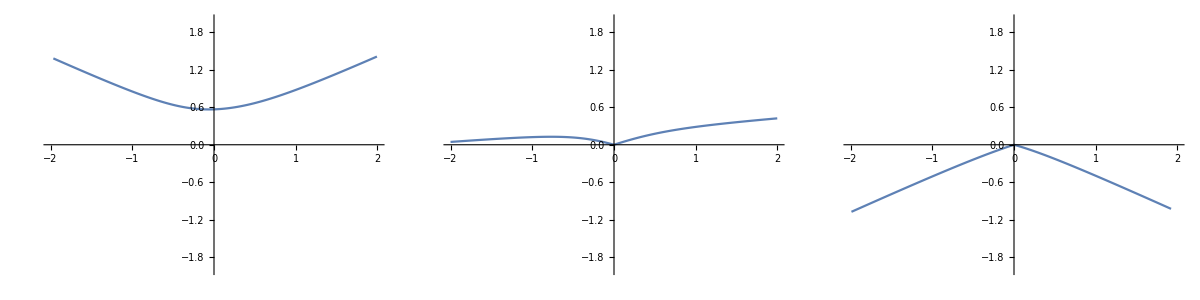

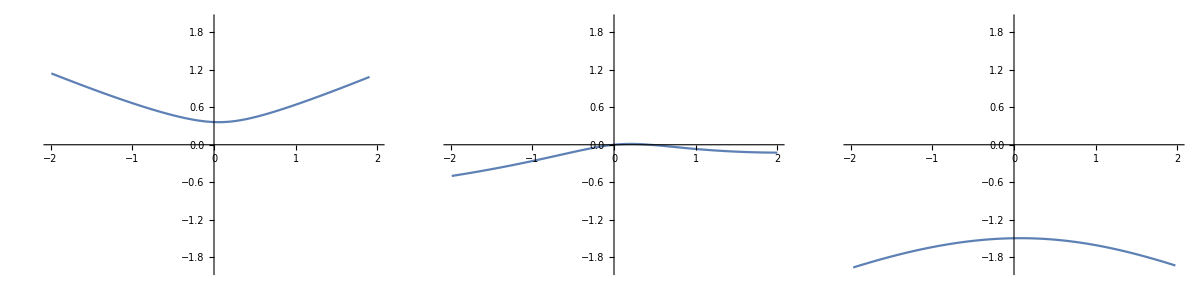

```mathematica
Grid@{{ListPlot[
SortBy[Select[spectDBWC1DRDBPltData,#[[2]]>0.5&&-2<#[[1]]<2&],First],PlotRange->{{-2,2},{-2,2}},Joined->True,ImageSize->Medium
],
ListPlot[
SortBy[Select[spectDBWC1DRDBPltData,0<#[[2]]<0.5&&-2<#[[1]]<2&],First],PlotRange->{{-2,2},{-2,2}},Joined->True,ImageSize->Medium
],
ListPlot[
SortBy[Select[spectDBWC1DRDBPltData,#[[2]]<0&&-2<#[[1]]<2&],First],PlotRange->{{-2,2},{-2,2}},Joined->True,ImageSize->Medium
]
}}

Grid@{{
ListPlot[
SortBy[Select[spectDBWC1DRDBMZAPltData,#[[2]]∈Reals&&#[[2]]>0.1&&-2<#[[1]]<2&],First]
,PlotRange->{{-2,2},{-2,2}},ImageSize->Medium,Joined->True
],
ListPlot[
SortBy[Select[spectDBWC1DRDBMZAPltData,#[[2]]∈Reals&&-1<#[[2]]<0.1&&-2<#[[1]]<2&],First]
,PlotRange->{{-2,2},{-2,2}},ImageSize->Medium,Joined->True
],
ListPlot[
SortBy[Select[spectDBWC1DRDBMZAPltData,#[[2]]∈Reals&&#[[2]]<-1&&-2<#[[1]]<2&],First]
,PlotRange->{{-2,2},{-2,2}},ImageSize->Medium,Joined->True
]
}}
```

```mathematica
Export["export/dr-db-three-beams/spectDB3WC1DRDBPltData-upper.csv",SortBy[Select[spectDBWC1DRDBPltData,#[[2]]>0.5&&-2<#[[1]]<2&],First]
]
Export["export/dr-db-three-beams/spectDB3WC1DRDBPltData-mid.csv",SortBy[Select[spectDBWC1DRDBPltData,0<#[[2]]<0.5&&-2<#[[1]]<2&],First]
]
Export["export/dr-db-three-beams/spectDB3WC1DRDBPltData-lower.csv",SortBy[Select[spectDBWC1DRDBPltData,#[[2]]<0&&-2<#[[1]]<2&],First]
]


Export["export/dr-db-three-beams/spectDB3WC1DRDBMZAPltData-upper.csv",SortBy[Select[spectDBWC1DRDBMZAPltData,#[[2]]∈Reals&&#[[2]]>0.1&&-2<#[[1]]<2&],First]
]
Export["export/dr-db-three-beams/spectDB3WC1DRDBMZAPltData-mid.csv",SortBy[Select[spectDBWC1DRDBMZAPltData,#[[2]]∈Reals&&-1<#[[2]]<0.1&&-2<#[[1]]<2&],First]
]
Export["export/dr-db-three-beams/spectDB3WC1DRDBMZAPltData-lower.csv",SortBy[Select[spectDBWC1DRDBMZAPltData,#[[2]]∈Reals&&#[[2]]<-1&&-2<#[[1]]<2&],First]
]
```

export/dr-db-three-beams/spectDB3WC1DRDBPltData-upper.csv

export/dr-db-three-beams/spectDB3WC1DRDBPltData-mid.csv

export/dr-db-three-beams/spectDB3WC1DRDBPltData-lower.csv

export/dr-db-three-beams/spectDB3WC1DRDBMZAPltData-upper.csv

export/dr-db-three-beams/spectDB3WC1DRDBMZAPltData-mid.csv

export/dr-db-three-beams/spectDB3WC1DRDBMZAPltData-lower.csv

```mathematica
Export["export/dr-db-three-beams/lsaMAARODataDB3WC1.csv",lsaMAARODataDBWC1 ]
```

export/dr-db-three-beams/lsaMAARODataDB3WC1.csv

#### C4

```mathematica
spectDBC4
```

{{-0.5,0.1},{1,0.4},{1,0.6}}

```mathematica
spectDBC4DRDBPltData=DBPltDRMAAData[spectDBC4,0.01];
spectDBC4DRDBMZAPltData=Flatten[DBPltDRMZAData[spectDBC4,0.01],1];
```

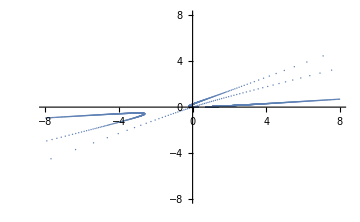

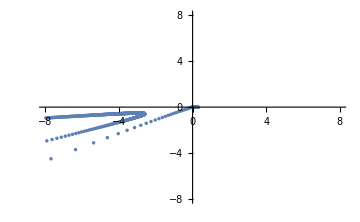

```mathematica
ListPlot[
SortBy[Select[spectDBC4DRDBPltData,-8<#[[1]]<8&],First],PlotRange->{{-8,8},{-8,8}},Joined->False,ImageSize->Medium
]

ListPlot[
SortBy[Select[spectDBC4DRDBPltData,-8<#[[1]]<8&&#[[2]]<0&],First],PlotRange->{{-8,8},{-8,8}},Joined->False,ImageSize->Medium
]
```

```mathematica
Export["export/dr-db-three-beams/spectDB3C4DRDBMAAPltData.csv",SortBy[Select[spectDBC4DRDBPltData,-8<#[[1]]<8&],First]
]

Export["export/dr-db-three-beams/spectDB3C4DRDBMZAPltData.csv",SortBy[Select[spectDBC4DRDBMZAPltData,#[[2]]∈Reals&&-8<#[[1]]<8&],First]
]
```

export/dr-db-three-beams/spectDB3C4DRDBMAAPltData.csv

export/dr-db-three-beams/spectDB3C4DRDBMZAPltData.csv

```mathematica
Sort[lsaMAARODataDBC4,#1[[2]]<#2[[2]]&]
```

{{-0.51,-2.90853,0.243194},{-0.46,-2.59982,0.623165},{-0.43,-2.41473,0.742244},{-0.42,-2.35306,0.774137},{-0.34,-1.86017,0.938487},{-0.33,-1.79862,0.950116},{-0.32,-1.73709,0.96007},{-0.31,-1.67557,0.968399},{-0.3,-1.61407,0.975142},{-0.28,-1.49111,0.98399},{-0.27,-1.42965,0.986132},{-0.26,-1.36821,0.986766},{-0.25,-1.30678,0.985892},{-0.24,-1.24537,0.983506},{-0.23,-1.18398,0.979594},{-0.22,-1.12261,0.974135},{-0.21,-1.06125,0.967102},{-0.19,-0.938587,0.948154},{-0.18,-0.877282,0.936136},{-0.15,-0.693476,0.889025},{-0.12,-0.509839,0.822929},{-0.1,-0.387511,0.76591},{-0.09,-0.326376,0.73264},{-0.08,-0.265261,0.695598},{-0.07,-0.204167,0.65414},{-0.06,-0.143092,0.607359},{-0.05,-0.0820385,0.553903},{-0.04,-0.0210054,0.491593},{0.,0.,0.1},{-0.03,0.0400068,0.41647},{-0.02,0.100998,0.319613},{-0.01,0.161968,0.166657}}

```mathematica
Export["export/dr-db-three-beams/lsaMAARODataDB3C4.csv",Sort[lsaMAARODataDBC4,#1[[2]]<#2[[2]]&]]
Export["export/dr-db-three-beams/lsaMZApRODataDB3C4.csv",Sort[lsaMZApRODataDBC4,#1[[2]]<#2[[2]]&]]
Export["export/dr-db-three-beams/lsaMZAmRODataDB3C4.csv",Sort[lsaMZAmRODataDBC4,#1[[2]]<#2[[2]]&]]
```

export/dr-db-three-beams/lsaMAARODataDB3C4.csv

export/dr-db-three-beams/lsaMZApRODataDB3C4.csv

export/dr-db-three-beams/lsaMZAmRODataDB3C4.csv

```mathematica
lsaMZApRODataDBC4
```

#### WC4

```mathematica
spectDBWC4
```

{{0.5,-0.1},{1,0.4},{1,0.6}}

```mathematica
spectDBWC4DRDBPltData=DBPltDRMAAData[spectDBWC4,0.01];
spectDBWC4DRDBMZAPltData=Flatten[DBPltDRMZAData[spectDBWC4,0.01],1];
```

```mathematica
Select[lsaMAARODataDBWC4,0.18<#[[1]]<0.22&]
Select[spectDBWC4DRDBPltData,-8<#[[1]]<8&&0.16<#[[2]]<0.24&]
Select[spectDBWC4DRDBPltData,-8<#[[1]]<8&&0.58<#[[2]]<0.62&]
```

{{0.19,-0.517908,0.977571},{0.2,-0.557106,0.966535},{0.21,-0.596327,0.951501}}

{{0.326538,0.166601},{0.423212,0.214829}}

{{-4.75848,0.617984},{-4.73501,0.615736},{-4.71174,0.613508},{-4.68867,0.6113},{-4.66579,0.609111},{-4.64311,0.606942},{-4.62062,0.604793},{-4.59831,0.602662},{-4.57619,0.60055},{-4.55426,0.598457},{-4.5325,0.596382},{-4.51093,0.594325},{-4.48953,0.592286},{-4.4683,0.590265},{-4.44725,0.588261},{-4.42637,0.586274},{-4.40565,0.584304},{-4.3851,0.582351},{-4.36472,0.580415},{0.238732,0.582274},{0.245729,0.58507},{0.252799,0.587905},{0.259943,0.59078},{0.267164,0.593697},{0.274461,0.596655},{0.281839,0.599657},{0.289297,0.602702},{0.296838,0.605792},{0.304464,0.608929},{0.312177,0.612112},{0.319978,0.615343},{0.32787,0.618623},{1.27272,0.617828}}

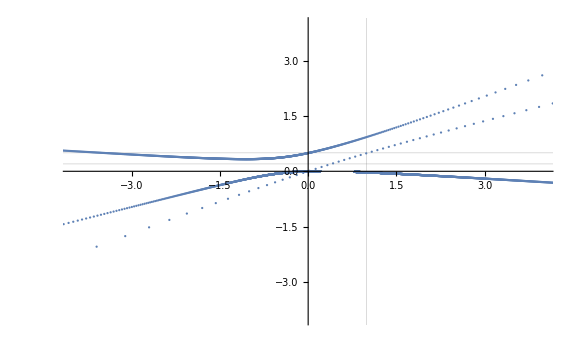

```mathematica
ListPlot[
SortBy[Select[spectDBWC4DRDBPltData,-8<#[[1]]<8&],First],PlotRange->{{-4,4},{-4,4}},Joined->False,ImageSize->Large,GridLines->{{0.99}, {0.2,0.5}}
]
```

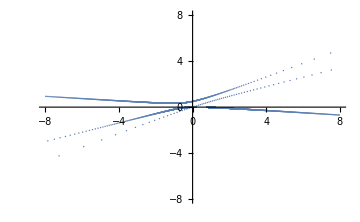

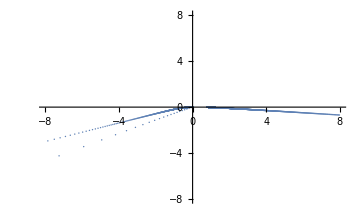

```mathematica
ListPlot[
SortBy[Select[spectDBWC4DRDBPltData,-8<#[[1]]<8&],First],PlotRange->{{-8,8},{-8,8}},Joined->False,ImageSize->Medium
]

ListPlot[
SortBy[Select[spectDBWC4DRDBPltData,-8<#[[1]]<8&&#[[2]]<0&],First],PlotRange->{{-8,8},{-8,8}},Joined->False,ImageSize->Medium
]
```

```mathematica
Export["export/dr-db-three-beams/spectDB3WC4DRDBMAAPltData.csv",SortBy[Select[spectDBWC4DRDBPltData,-8<#[[1]]<8&],First]
]

Export["export/dr-db-three-beams/spectDB3WC4DRDBMZAPltData.csv",SortBy[Select[spectDBWC4DRDBMZAPltData,#[[2]]∈Reals&&-8<#[[1]]<8&],First]
]
```

export/dr-db-three-beams/spectDB3WC4DRDBMAAPltData.csv

export/dr-db-three-beams/spectDB3WC4DRDBMZAPltData.csv

```mathematica
Sort[lsaMAARODataDBWC4,#1[[2]]<#2[[2]]&]
```

{{0.32,-1.02924,0.321337},{0.31,-0.989772,0.461254},{0.3,-0.950325,0.561215},{0.29,-0.9109,0.640211},{0.28,-0.871499,0.705316},{0.27,-0.83212,0.760102},{0.26,-0.792765,0.806669},{0.25,-0.753432,0.84637},{0.24,-0.714122,0.88013},{0.23,-0.674835,0.908606},{0.22,-0.63557,0.932278},{0.21,-0.596327,0.951501},{0.2,-0.557106,0.966535},{0.19,-0.517908,0.977571},{0.18,-0.478731,0.984738},{0.17,-0.439576,0.988116},{0.16,-0.400442,0.98774},{0.15,-0.36133,0.983603},{0.14,-0.322239,0.975651},{0.13,-0.283169,0.963787},{0.12,-0.24412,0.94786},{0.11,-0.205091,0.927657},{0.1,-0.166083,0.902886},{0.09,-0.127096,0.873155},{0.08,-0.0881278,0.837931},{0.07,-0.0491799,0.796481},{0.06,-0.0102517,0.747767},{0.,0.,0.1},{0.05,0.0286571,0.690247},{0.04,0.0675466,0.621474},{0.03,0.106417,0.537139},{0.02,0.145269,0.428134},{0.01,0.184102,0.265639}}

```mathematica
lsaMZAmRODataDBWC4=Drop[SortBy[LSAMZAmRODataDB[LSAMZAmRODataRawDB[spectDBWC4,{-4,4,0.001}],Symbol["spectDB"<>"WC4"] ,0.01,0.01],Last],-1];//Quiet
```

```mathematica
Export["export/dr-db-three-beams/lsaMAARODataDB3WC4.csv",Sort[lsaMAARODataDBWC4,#1[[2]]<#2[[2]]&]]
Export["export/dr-db-three-beams/lsaMZApRODataDB3WC4.csv",Sort[lsaMZApRODataDBWC4,#1[[2]]<#2[[2]]&]]
Export["export/dr-db-three-beams/lsaMZAmRODataDB3WC4.csv",Sort[lsaMZAmRODataDBWC4,#1[[2]]<#2[[2]]&]]
```

export/dr-db-three-beams/lsaMAARODataDB3WC4.csv

export/dr-db-three-beams/lsaMZApRODataDB3WC4.csv

export/dr-db-three-beams/lsaMZAmRODataDB3WC4.csv

## Calculate DR

Plots

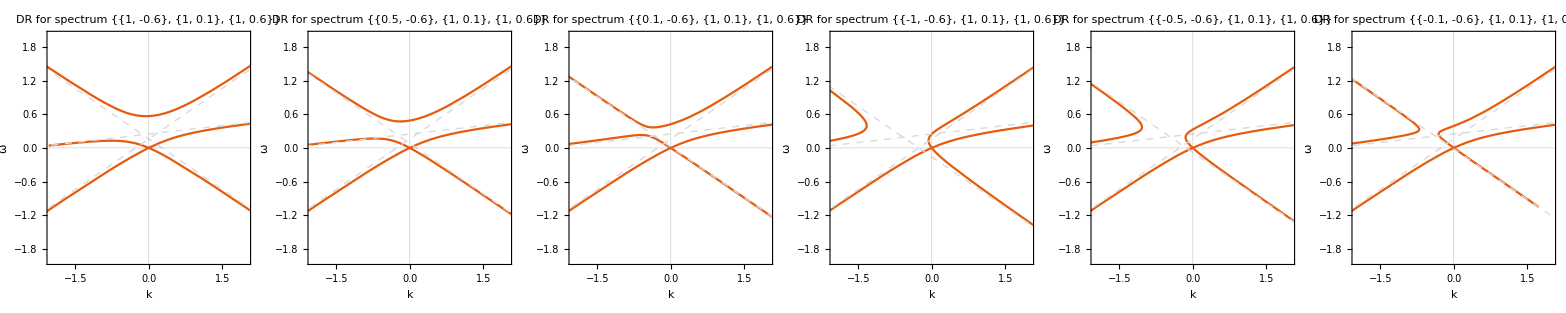

```mathematica
Grid@{
{pltDRMAADBWC1,pltDRMAADBWC2,pltDRMAADBWC3,pltDRMAADBC1,pltDRMAADBC2,pltDRMAADBC3}=Table[
DBPltDRMAA[spectra,{{-2,2},{-2,2}}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
]
}
```

```mathematica
Grid@{
{pltDRMZADBWC1,pltDRMZADBWC2,pltDRMZADBWC3,pltDRMZADBC1,pltDRMZADBC2,pltDRMZADBC3}=Table[
DBPltDRMZA[spectra,{{-4,4},{-4,4}}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
]
}
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Plot C4 and WC4

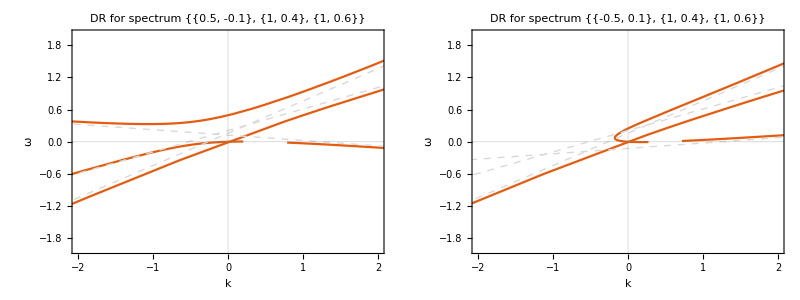

```mathematica
Grid@{
{pltDRMAADBWC4,pltDRMAADBC4}=Table[
DBPltDRMAA[spectra,{{-2,2},{-2,2}}],
{spectra,{spectDBWC4,spectDBC4}}
]
}
```

```mathematica
Grid@{
{pltDRMZADBWC4,pltDRMZADBC4}=Table[
DBPltDRMZA[spectra,{{-2,2},{-2,2}}],
{spectra,{spectDBWC4,spectDBC4}}
]
}
```

-Graphics- | -Graphics-

## Calculate Instability

Real Omega MAA

```mathematica
Table[
Symbol["lsaMAARODataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","WC4","C1","C2","C3","C4"}}
]
```

{lsaMAARODataRawDBWC1,lsaMAARODataRawDBWC2,lsaMAARODataRawDBWC3,lsaMAARODataRawDBWC4,lsaMAARODataRawDBC1,lsaMAARODataRawDBC2,lsaMAARODataRawDBC3,lsaMAARODataRawDBC4}

```mathematica
{lsaMAARODataRawDBWC1,lsaMAARODataRawDBWC2,lsaMAARODataRawDBWC3,lsaMAARODataRawDBWC4,lsaMAARODataRawDBC1,lsaMAARODataRawDBC2,lsaMAARODataRawDBC3,lsaMAARODataRawDBC4}= Table[
LSAMAARODataRawDB[spectra,{-4,4,0.01}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBWC4,spectDBC1,spectDBC2,spectDBC3,spectDBC4}}
];
```

```mathematica
lsaMAARODataDBList=Table[
LSAMAARODataDB[Symbol["lsaMAARODataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ],
{spectraid,{"WC1","WC2","WC3","WC4","C1","C2","C3","C4"}}
];
```

```mathematica
{lsaMAARODataDBWC1,lsaMAARODataDBWC2,lsaMAARODataDBWC3,lsaMAARODataDBWC4,lsaMAARODataDBC1,lsaMAARODataDBC2,lsaMAARODataDBC3,lsaMAARODataDBC4}=lsaMAARODataDBList;
```

```mathematica
lsaMAAROPltDBList=Table[
pltDROmegaRealLSA[
Symbol["lsaMAARODataDB"<>spectraid],Symbol["pltDRMAADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","WC4","C1","C2","C3","C4"}}
];
```

```mathematica
Grid@{lsaMAAROPltDBList[[;;]]}
```

-Graphics-

```mathematica
(*Export["lsaMAAROPltDB-C1-to-C3.png",Out[69]]*)
```

```mathematica
Grid@{{lsaMAAROPltDBList[[4]],
lsaMAAROPltDBList[[8]]}}
```

-Graphics-

```mathematica
Export[
"lsaMAAROPltDB-WC4-and-C4.png",

]
```

lsaMAAROPltDB-WC4-and-C4.png

```mathematica
spectDBC4
spectDBWC4
```

{{-0.5,0.1},{1,0.4},{1,0.6}}

{{0.5,-0.1},{1,0.4},{1,0.6}}

Real Omega MZAp

Generate the variable names

```mathematica
Table[
Symbol["lsaMZApRODataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","WC4","C1","C2","C3","C4"}}
]
```

{lsaMZApRODataRawDBWC1,lsaMZApRODataRawDBWC2,lsaMZApRODataRawDBWC3,lsaMZApRODataRawDBWC4,lsaMZApRODataRawDBC1,lsaMZApRODataRawDBC2,lsaMZApRODataRawDBC3,lsaMZApRODataRawDBC4}

```mathematica
Table[
Symbol["lsaMZApRODataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","WC4","C1","C2","C3","C4"}}
]
```

{lsaMZApRODataDBWC1,lsaMZApRODataDBWC2,lsaMZApRODataDBWC3,lsaMZApRODataDBWC4,lsaMZApRODataDBC1,lsaMZApRODataDBC2,lsaMZApRODataDBC3,lsaMZApRODataDBC4}

Calculate the instabilities

```mathematica
{lsaMZApRODataRawDBWC1,lsaMZApRODataRawDBWC2,lsaMZApRODataRawDBWC3,lsaMZApRODataRawDBWC4,lsaMZApRODataRawDBC1,lsaMZApRODataRawDBC2,lsaMZApRODataRawDBC3,lsaMZApRODataRawDBC4}= Table[
LSAMZApRODataRawDB[spectra,{-4,4,0.01}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBWC4,spectDBC1,spectDBC2,spectDBC3,spectDBC4}}
];//Quiet
```

```mathematica
lsaMZApRODataDBList=Table[
LSAMZApRODataDB[Symbol["lsaMZApRODataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] , 0.01,0.01],
{spectraid,{"WC1","WC2","WC3","WC4","C1","C2","C3","C4"}}
];
```

```mathematica
{lsaMZApRODataDBWC1,lsaMZApRODataDBWC2,lsaMZApRODataDBWC3,lsaMZApRODataDBWC4,lsaMZApRODataDBC1,lsaMZApRODataDBC2,lsaMZApRODataDBC3,lsaMZApRODataDBC4}=lsaMZApRODataDBList;
```

```mathematica
lsaMZApROPltDBList=Table[
pltDROmegaRealLSA[
Symbol["lsaMZApRODataDB"<>spectraid],Symbol["pltDRMZADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","WC4","C1","C2","C3","C4"}}
];
```

```mathematica
Grid@{lsaMZApROPltDBList[[4;;]]}
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*Export["lsaMZApROPltDB-C1-to-C3.png",Out[105]]*)
```

```mathematica
Grid@{{lsaMZApROPltDBList[[4]],
lsaMZApROPltDBList[[8]]}}
```

-Graphics- | -Graphics-

```mathematica
Export[
"lsaMZApROPltDB-WC4-and-C4.png",

]
```

lsaMZApROPltDB-WC4-and-C4.png

Real Omega MZAm

Generate the variable names

```mathematica
Table[
Symbol["lsaMZAmRODataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","WC4","C1","C2","C3","C4"}}
]
```

{lsaMZAmRODataRawDBWC1,lsaMZAmRODataRawDBWC2,lsaMZAmRODataRawDBWC3,lsaMZAmRODataRawDBWC4,lsaMZAmRODataRawDBC1,lsaMZAmRODataRawDBC2,lsaMZAmRODataRawDBC3,lsaMZAmRODataRawDBC4}

```mathematica
Table[
Symbol["lsaMZAmRODataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","WC4","C1","C2","C3","C4"}}
]
```

{lsaMZAmRODataDBWC1,lsaMZAmRODataDBWC2,lsaMZAmRODataDBWC3,lsaMZAmRODataDBWC4,lsaMZAmRODataDBC1,lsaMZAmRODataDBC2,lsaMZAmRODataDBC3,lsaMZAmRODataDBC4}

Calculate the instabilities

```mathematica
{lsaMZAmRODataRawDBWC1,lsaMZAmRODataRawDBWC2,lsaMZAmRODataRawDBWC3,lsaMZAmRODataRawDBWC4,lsaMZAmRODataRawDBC1,lsaMZAmRODataRawDBC2,lsaMZAmRODataRawDBC3,lsaMZAmRODataRawDBC4}= Table[
LSAMZAmRODataRawDB[spectra,{-4,4,0.01}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBWC4,spectDBC1,spectDBC2,spectDBC3,spectDBC4}}
];//Quiet
```

```mathematica
lsaMZAmRODataDBList=Table[
LSAMZAmRODataDB[Symbol["lsaMZAmRODataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ,0.01,0.01],
{spectraid,{"WC1","WC2","WC3","WC4","C1","C2","C3","C4"}}
];
```

```mathematica
{lsaMZAmRODataDBWC1,lsaMZAmRODataDBWC2,lsaMZAmRODataDBWC3,lsaMZAmRODataDBWC4,lsaMZAmRODataDBC1,lsaMZAmRODataDBC2,lsaMZAmRODataDBC3,lsaMZAmRODataDBC4}=lsaMZAmRODataDBList;
```

```mathematica
lsaMZAmROPltDBList=Table[
pltDROmegaRealLSA[
Symbol["lsaMZAmRODataDB"<>spectraid],Symbol["pltDRMZADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","WC4","C1","C2","C3","C4"}}
];
```

```mathematica
Grid@{lsaMZAmROPltDBList[[5;;]]}
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*Export["lsaMZAmROPltDB-C1-to-C3.png",Out[125]]*)
```

```mathematica
Grid@{{lsaMZAmROPltDBList[[4]],
lsaMZAmROPltDBList[[8]]}}
```

-Graphics- | -Graphics-

```mathematica
Export[
"lsaMZAmROPltDB-WC4-and-C4.png",
%
]
```

lsaMZAmROPltDB-WC4-and-C4.png

Real k MAA

Generate the variable names for real k (MAA) solution

```mathematica
Table[
Symbol["lsaMAARKDataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMAARKDataRawDBWC1,lsaMAARKDataRawDBWC2,lsaMAARKDataRawDBWC3,lsaMAARKDataRawDBC1,lsaMAARKDataRawDBC2,lsaMAARKDataRawDBC3}

```mathematica
Table[
Symbol["lsaMAARKDataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMAARKDataDBWC1,lsaMAARKDataDBWC2,lsaMAARKDataDBWC3,lsaMAARKDataDBC1,lsaMAARKDataDBC2,lsaMAARKDataDBC3}

Calculate the instabilities

```mathematica
{lsaMAARKDataRawDBWC1,lsaMAARKDataRawDBWC2,lsaMAARKDataRawDBWC3,lsaMAARKDataRawDBC1,lsaMAARKDataRawDBC2,lsaMAARKDataRawDBC3}= Table[
LSAMAARKDataRawDB[spectra,{-4,4,0.1}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
];
```

```mathematica
lsaMAARKDataDBList=Table[
LSAMAARKDataDB[Symbol["lsaMAARKDataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ,0.01,0.01],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
{lsaMAARKDataDBWC1,lsaMAARKDataDBWC2,lsaMAARKDataDBWC3,lsaMAARKDataDBC1,lsaMAARKDataDBC2,lsaMAARKDataDBC3}=lsaMAARKDataDBList;
```

```mathematica
lsaMAARKPltDBList=Table[
pltDRKRealLSA[
Symbol["lsaMAARKDataDB"<>spectraid],Symbol["pltDRMAADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
Grid@{lsaMAARKPltDBList[[4;;]]}
```

-Graphics-

```mathematica
(*Export["lsaMAARKPltDB-WC1-to-WC3-and-C1-to-C3.png",Out[212]]*)
```

Real k MZAp

```mathematica
Table[
Symbol["lsaMZApRKDataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZApRKDataRawDBWC1,lsaMZApRKDataRawDBWC2,lsaMZApRKDataRawDBWC3,lsaMZApRKDataRawDBC1,lsaMZApRKDataRawDBC2,lsaMZApRKDataRawDBC3}

```mathematica
Table[
Symbol["lsaMZApRKDataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZApRKDataDBWC1,lsaMZApRKDataDBWC2,lsaMZApRKDataDBWC3,lsaMZApRKDataDBC1,lsaMZApRKDataDBC2,lsaMZApRKDataDBC3}

Calculate the instabilities

```mathematica
{lsaMZApRKDataRawDBWC1,lsaMZApRKDataRawDBWC2,lsaMZApRKDataRawDBWC3,lsaMZApRKDataRawDBC1,lsaMZApRKDataRawDBC2,lsaMZApRKDataRawDBC3}= Table[
LSAMZApRKDataRawDB[spectra,{-4,4,0.1}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
];
```

Last::normal: Nonatomic expression expected at position 1 in Last[omega].

General::stop: Further output of Last :: normal will be suppressed during this calculation.

```mathematica
lsaMZApRKDataDBList=Table[
LSAMZApRKDataDB[Symbol["lsaMZApRKDataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ,0.01,0.001],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
{lsaMZApRKDataDBWC1,lsaMZApRKDataDBWC2,lsaMZApRKDataDBWC3,lsaMZApRKDataDBC1,lsaMZApRKDataDBC2,lsaMZApRKDataDBC3}=lsaMZApRKDataDBList;
```

```mathematica
lsaMZApRKPltDBList=Table[
pltDRKRealLSA[
Symbol["lsaMZApRKDataDB"<>spectraid],Symbol["pltDRMZADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
Grid@{lsaMZApRKPltDBList[[;;3]],lsaMZApRKPltDBList[[4;;]]}
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Export["lsaMZApRKPltDB-WC1-to-WC3-and-C1-to-C3.png",Out[263]]*)
```

Real k MZAm

```mathematica
Table[
Symbol["lsaMZAmRKDataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZAmRKDataRawDBWC1,lsaMZAmRKDataRawDBWC2,lsaMZAmRKDataRawDBWC3,lsaMZAmRKDataRawDBC1,lsaMZAmRKDataRawDBC2,lsaMZAmRKDataRawDBC3}

```mathematica
Table[
Symbol["lsaMZAmRKDataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZAmRKDataDBWC1,lsaMZAmRKDataDBWC2,lsaMZAmRKDataDBWC3,lsaMZAmRKDataDBC1,lsaMZAmRKDataDBC2,lsaMZAmRKDataDBC3}

Calculate the instabilities

```mathematica
{lsaMZAmRKDataRawDBWC1,lsaMZAmRKDataRawDBWC2,lsaMZAmRKDataRawDBWC3,lsaMZAmRKDataRawDBC1,lsaMZAmRKDataRawDBC2,lsaMZAmRKDataRawDBC3}= Table[
LSAMZAmRKDataRawDB[spectra,{-4,4,0.1}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
];
```

Last::normal: Nonatomic expression expected at position 1 in Last[omega].

General::stop: Further output of Last :: normal will be suppressed during this calculation.

```mathematica
lsaMZAmRKDataDBList=Table[
LSAMZAmRKDataDB[Symbol["lsaMZAmRKDataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ,0.01,0.001],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
{lsaMZAmRKDataDBWC1,lsaMZAmRKDataDBWC2,lsaMZAmRKDataDBWC3,lsaMZAmRKDataDBC1,lsaMZAmRKDataDBC2,lsaMZAmRKDataDBC3}=lsaMZAmRKDataDBList;
```

```mathematica
lsaMZAmRKPltDBList=Table[
pltDRKRealLSA[
Symbol["lsaMZAmRKDataDB"<>spectraid],Symbol["pltDRMZADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
Grid@{lsaMZAmRKPltDBList[[;;3]],lsaMZAmRKPltDBList[[4;;]]}
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*Export["lsaMZAmRKPltDB-WC1-to-WC3-and-C1-to-C3.png",Out[273]]*)
```